```mathematica
SetDirectory[NotebookDirectory[]];
Get["Kimberling.m"];
```

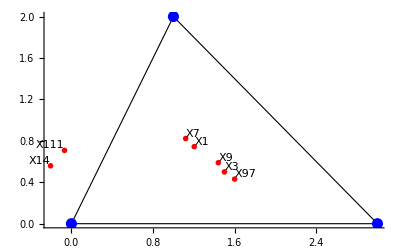

{{(3 (5+√5))/(5+3 √5+2 √10),(6 √5)/(5+3 √5+2 √10)},{3/2,1/2},{(2 (-10+9 √2+√10))/(-11+6 √2+3 √5+2 √10),(4 (-1+√10))/(-11+6 √2+3 √5+2 √10)},{(3 (-4+√2+2 √5+√10))/(-11+6 √2+3 √5+2 √10),(15-9 √5+6 √10)/(15+10 √2-11 √5+6 √10)},{1/13 (6-5 √3),1/13 (9-√3)},{8/5,28/65},{-6/89,63/89}}

```mathematica
PA={0,0}; PB={3,0}; PC={1,2};
indices = {1,3,7,9,14,97, 111};
centers =Table[KimberlingCenter[i,PA,PB,PC],{i,indices}]//Simplify;
names=Table["X"<>TextString[n],{n,indices}];
Graphics[Join[
{EdgeForm[{Thin, Black}], FaceForm[], Triangle[{PA,PB,PC}]},
{{PA, PB, PC}/.{x_,y_}:>{Blue,PointSize[0.02],Point[{x,y}]}},
{centers/.{x_,y_}:>{Red,PointSize[0.01],Point[{x,y}]}},
Text[#[[1]],#[[2]],-1.5 Sign@#[[2]]]&/@Transpose@{names, centers}
], AspectRatio->Automatic, Axes-> True
]
centers
```